### Categorization

Tutorial

NounouM2

NounouM2`

NounouM2/tutorial/Load MiCam images (.GSD) and plot

### Keywords

Details

# Load MiCam images (.GSD) and plot

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

Initialize Package

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

( last updated:  Tue 4 Mar 2014 14:44:15 )

( current Git HEAD:  c1b623a1c1f703ddee3ec7367c20c50915fc6ff2 )

( http://github.org/ktakagaki/nounoum )

<<Set JLink` java stack size to 6144Mb>>

```mathematica
(*This will allow one to see logging traces and errors*)
(*On windows, the content of these logs will be output to the default user directory as a text file*)
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

Load Data Files

```mathematica
nnDataDirectory = "E:\\data\\Micam\\dc-stimulation\\140224"
```

E:\data\Micam\dc-stimulation\140224

```mathematica
(*The $NNReader object is initialized by default upon calling <<NounouM2`*)
(*The object starts out empty*)
(*Further reader objects can be created, using the Java constructor, but beware of having too many readers with too many open data files---and running out of memory*)
$NNReader@load[nnDataDirectory<>"\\mag140224006A.gsd"]
```

Java::excptn: A Java exception occurred: "java.lang.IndexOutOfBoundsException: (7360,0) not in [-7360,7360) x [-15000,15000)\n\tat breeze.linalg.DenseMatrix$mcI$sp.update$mcI$sp(DenseMatrix.scala:95)\n\tat nounou.data.io.FileAdapterGSDGSH$.loadImplGSD(FileAdapterGSDGSH.scala:142)\n\tat nounou.data.io.FileAdapterGSDGSH$.loadImpl(FileAdapterGSDGSH.scala:26)\n\tat nounou.data.io.FileAdapter$$anon$1.apply(FileAdapter.scala:60)\n\tat nounou.data.io.FileAdapter$$anon$1.apply(FileAdapter.scala:59)\n\tat nounou.data.io.FileAdapter$class.load(FileAdapter.scala:56)\n\tat nounou.data.io.FileAdapterGSDGSH$.load(FileAdapterGSDGSH.scala:15)\n\tat nounou.DataReader.load(DataReader.scala:184)\n\tat nounou.DataReader.load(DataReader.scala:193)".

$Failed

```mathematica
ListLinePlot[$NNReader@data[]@readTraceAbsA[62*92+42-1, NN`frameRangeAll[]],PlotRange->All, AspectRatio->1/5, ImageSize->72*8]
```

Java::excptn: A Java exception occurred: "java.lang.IndexOutOfBoundsException: 0\n\tat scala.collection.immutable.Vector.checkRangeConvert(Vector.scala:137)\n\tat scala.collection.immutable.Vector.apply(Vector.scala:127)\n\tat nounou.data.traits.XFrames$class.isRealisticFrameRange(XFrames.scala:61)\n\tat nounou.data.XData.isRealisticFrameRange(XData.scala:14)\n\tat nounou.data.XData.readTrace(XData.scala:112)\n\tat nounou.data.XData.readTrace(XData.scala:105)\n\tat nounou.data.XData.readTraceAbs(XData.scala:157)\n\tat nounou.data.XData.readTraceAbsA(XData.scala:164)".

ListLinePlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[$Failed,PlotRange→All,AspectRatio→1/5,ImageSize→576]

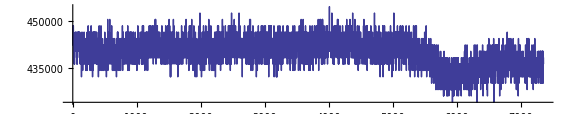

```mathematica
ListLinePlot[$NNReader@dataORI[]@readTraceAbsA[62*92+42-1, NN`frameRangeAll[]],PlotRange->All, AspectRatio->1/5, ImageSize->72*8]
```

More About

Related Tutorials

Related Wolfram Education Group Courses